## ^135Pr - experimental wobbling spectra

## Sensharma et al. 2019 Energies in keV

## Gammas (between band states) - γ

```mathematica
γ0={372.9,659.8,854.3,999.7,1075.6,843.7,834.3,882.2,922.4,957.0,1005.0};
e0=358.0;
gs=e0+γ0[[1]];(*ground-state band for the TW1 and TW2 decay*)
e01=gs+746.6;(*band head for TW1*)
e02=gs+1197.1;(*band head for TW2*)
γ1={726.5,795.7,955.7,1111.7};
γ2={826.6,763.8,1009.0};
```

## Energies (experimental - excitation energies)

### imported from C++ (normalized to the first state from YRAST0

```mathematica
y0={0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069};
tw1={0.7466,1.4731,2.2688,3.2245,4.3362};
tw2={1.1971,2.0237,2.7875,3.7965};
energiesExp=Join[y0,tw1,tw2];
```

```mathematica
energiesExp
```

{0.3729,1.0327,1.887,2.8867,3.9623,4.806,5.6403,6.5225,7.4449,8.4019,9.4069,0.7466,1.4731,2.2688,3.2245,4.3362,1.1971,2.0237,2.7875,3.7965}

## Spins (experimental)

```mathematica
spin0={7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5};
spin1={8.5,10.5,12.5,14.5,16.5};
spin2={9.5,11.5,13.5,15.5};
spins=Join[spin0,spin1,spin2];
```

```mathematica
spins
```

{7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,8.5,10.5,12.5,14.5,16.5,9.5,11.5,13.5,15.5}

## Energy formulas

```mathematica
omega[spin_,j_,θ_,a1_,a2_,a3_]:=(((2spin+1)*(a2-a1-(a2*j*Sin[θ*π/180])/spin)-2a1*j*Cos[θ*π/180])*((2spin+1)*(a3-a1)-2*a1*j*Cos[θ*π/180])-(a3-a1)*(a2-a1-(a2*j*Sin[θ*π/180])/spin))^(1/2);
hmin[spin_,j_,θ_,a1_,a2_,a3_]:=a1*spin^2+(2spin+1)*a1*j*Cos[θ*π/180]-spin*a2*j*Sin[θ*π/180]+(a1*(j*Cos[θ*π/180])^2+a2*(j*Sin[θ*π/180])^2);
energy[n_,spin_,j_,θ_,a1_,a2_,a3_]:=hmin[spin,j,θ,a1,a2,a3]+(n+1/2)*omega[spin,j,θ,a1,a2,a3];
```

## Define the bands - theoretical formulation

```mathematica
eZero[θ_,a1_,a2_,a3_]:=energy[0,5.5,5.5,θ,a1,a2,a3];
yrastI[spin_,j_,θ_,a1_,a2_,a3_]:=energy[0,spin,j,θ,a1,a2,a3]-eZero[θ,a1,a2,a3];
wobb1I[spin_,j_,θ_,a1_,a2_,a3_]:=energy[0,spin,j,θ,a1,a2,a3]-eZero[θ,a1,a2,a3];
wobb2I[spin_,j_,θ_,a1_,a2_,a3_]:=energy[1,spin-1,j,θ,a1,a2,a3]-eZero[θ,a1,a2,a3];
```

## Construct the theoretical dataset based on the fit params

```mathematica
(*PARAMS = { θ, Subscript[ℐ, 1], Subscript[ℐ, 2], Subscript[ℐ, 3]}*)
```

```mathematica
params={-71,1/(2*89),1/(2*12),1/(2*48)};
oddspin=5.5;
```

```mathematica
y0Th=Table[yrastI[spin0[[i]],oddspin,params[[1]],params[[2]],params[[3]],params[[4]]],{i,1,Length[spin0]}];
tw1Th=Table[wobb1I[spin1[[i]],oddspin,params[[1]],params[[2]],params[[3]],params[[4]]],{i,1,Length[spin1]}];
tw2Th=Table[wobb2I[spin2[[i]],oddspin,params[[1]],params[[2]],params[[3]],params[[4]]],{i,1,Length[spin2]}];
energiesTh=Join[y0Th,tw1Th,tw2Th];
```

## Rms calculation

```mathematica
rms[dataexp_,datath_]:=√(Sum[(dataexp[[i]]-datath[[i]])^2,{i,1,Length[dataexp]}]/(Length[dataexp]+1));
```

```mathematica
rms[energiesExp,energiesTh]
```

0.174452

## Graphical representation

```mathematica
plotband[spvals_,envals_,color_,legend_]:=ListPlot[Table[{spvals[[i]],envals[[i]]},{i,1,Length[spvals]}],Joined->True,Frame->True,PlotMarkers->{Automatic, Medium},PlotStyle->{color},FrameStyle->Directive[Black,Thick],LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{legend},{0.75,0.25}],FrameLabel->{"I [ℏ]","E [MeV]"},Axes->False];
```

## yrast band

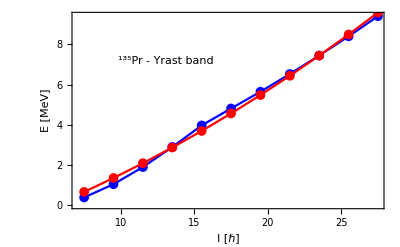

```mathematica
Show[plotband[spin0,y0,Blue,"exp"],plotband[spin0,y0Th,Red,"th"],Epilog->Inset[Framed[Style["^135Pr - Yrast band",20,Italic,Bold,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.30,0.75}]]]
```

## one-phonon band

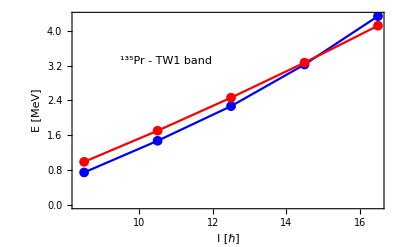

```mathematica
Show[plotband[spin1,tw1,Blue,"exp"],plotband[spin1,tw1Th,Red,"th"],Epilog->Inset[Framed[Style["^135Pr - TW1 band",20,Italic,Bold,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.30,0.75}]]]
```

## two-phonon band

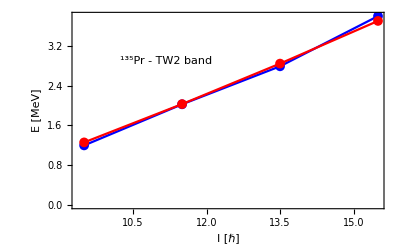

```mathematica
Show[plotband[spin2,tw2,Blue,"exp"],plotband[spin2,tw2Th,Red,"th"],Epilog->Inset[Framed[Style["^135Pr - TW2 band",20,Italic,Bold,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.30,0.75}]]]
```

## Wobbling frequencies

```mathematica
spiner=Table[i,{i,7.5,55.5,2}];
omegas[angle_]:=Table[omega[spiner[[i]],oddspin,angle,params[[2]],params[[3]],params[[4]]],{i,1,Length[spiner]}];
```

```mathematica
spiner
```

{7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5,47.5,49.5,51.5,53.5,55.5}

```mathematica
omegas[-71]
```

omegas[-71]

```mathematica
plotband[spvals_,envals_,color_,legend_]:=ListPlot[Table[{spvals[[i]],envals[[i]]},{i,1,Length[spvals]}],Joined->True,Frame->True,PlotMarkers->{Automatic, Medium},PlotStyle->{color},FrameStyle->Directive[Black,Thick],LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{legend},{0.75,0.25}],FrameLabel->{"I [ℏ]","ω [MeV]"},Axes->False];
```

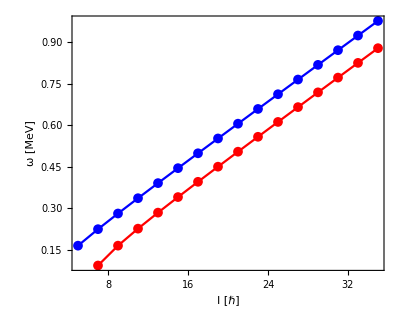

```mathematica
Show[plotband[spiner,omegas[-71],Blue,"θ=-71^o"],plotband[spiner,omegas[109],Red,"θ=109^o"],(*Epilog->Inset[Framed[Style["ω^I",20,Italic,Bold,FontFamily->"Times New Roman"],Background->None,FrameStyle->White],Scaled[{0.30,0.75}]]*)PlotRange->Automatic,AspectRatio->0.8]
```

```mathematica
Do[Print[spins[[i]]," ",omega[spins[[i]],oddspin,params[[1]],params[[2]],params[[3]],params[[4]]]],{i,1,Length[spins]}]
```

7.5 0.239624

9.5 0.295775

11.5 0.35077

13.5 0.405102

15.5 0.459018

17.5 0.512653

19.5 0.566089

21.5 0.619381

23.5 0.672562

25.5 0.725658

27.5 0.778687

8.5 0.267893

10.5 0.323378

12.5 0.378

14.5 0.432102

16.5 0.485864

9.5 0.295775

11.5 0.35077

13.5 0.405102

15.5 0.459018